```mathematica
<<MaTeX`
nbOfFamilies =1;
machineZero = 10^(-$MachinePrecision);
```

## Fermion and Boson Basis functions S, L, SR, CR, SL, CL

```mathematica
(*Bessel basis functions Subscript[FHat, αβ],Subscript[F, αβ] *)
Fab[α_, β_, u_, v_]:=BesselJ[α, u] BesselY[β, v] - BesselY[α, u]BesselJ[β, v];
FHat[α_, β_, u_, v_]:=BesselI[α, u] * BesselK[β, v] - Exp[-ⅈ(α - β ) * Pi] * BesselK[α,u] * BesselI[β,v];
FHatcPM[q_, c_, pm1_, pm2_, zL_]:=FHat[ c + pm1*1/2, c+pm2*1/2, q*(zL^(-1)), q  ];
(*   Fermions  *)
SL[λ_, z_, zL_, c_]:=-π/2 λ Sqrt[z zL]Fab[c+1/2, c+1/2, λ z, λ zL];
SR[λ_, z_, zL_, c_]:= (+π)/2 λ Sqrt[z zL]Fab[c-1/2, c-1/2, λ z, λ zL];
CR[λ_, z_, zL_, c_]:=-π/2 λ Sqrt[z zL]Fab[c-1/2, c+1/2, λ z, λ zL];
CL[λ_, z_, zL_, c_]:=(+π)/2 λ Sqrt[z zL]Fab[c+1/2, c-1/2, λ z, λ zL];



(*   Bosons   *)
Cbasis[λ_, z_, zL_]:=π/2 λ (z^(3/2)) (zL^(1/2)) Fab[3/2, 1/2, λ z, λ zL];
Sbasis[λ_, z_, zL_]:=-π/2 λ (z^(3/2)) (zL^(1/2)) Fab[3/2, 3/2, λ z ,λ zL];
Cprime[λ_, z_, zL_]:=π/2(λ^2) (z^(3/2)) (zL^(1/2)) Fab[1/2, 1/2, λ z, λ zL];
Sprime[λ_, z_, zL_]:=-π/2(λ^2) (z^(3/2)) (zL^(1/2))Fab[1/2, 3/2, λ z, λ zL];
```

## Mass Approximations

```mathematica
mWboson[k_, zL_, θH_]:=Sqrt[3/2] * k *((zL)^(-3/2)) * Sin[θH];
mZboson[mWboson_, sin2θW_]:=mWboson / Sqrt[1-sin2θW];
muTypeQuark[c0_, k_, zL_,θH_ ]:=If[c0< 0.5,
 (k/zL )*Sqrt[1 - 4 (c0)^2]Sin[θH/2],
 k *((zL)^-1/2 - c0)*Sqrt[4(c0)^2 - 1]Sin[θH/2]
];
mdTypeQuark[c0_, c1_, μ11_, μ1_, k_, zL_, θH_]:=If[c0<0.5,
k * ((zL)^(c0-c1-1)) * μ11/μ1*Sqrt[(1-2c0)(1+2c1)]*Sin[θH/2],
k * ((zL)^(-c1-1/2)) * μ11/μ1*Sqrt[(2c0 - 1)(2c1 + 1)]*Sin[θH/2]
];
meTypeLepton[c2_, c0_, μ11Prime_, μ2Tilde_, k_, zL_, θH_]:=If[ c2<0.5,
k * ((zL)^(-1+c2-c0)) * μ11Prime/μ2Tilde Sqrt[(2c0 + 1)(1-2c2)]Sin[θH/2],
k *  ((zL)^(-1/2 - c0)) * μ11Prime/μ2Tilde Sqrt[(2c0+1)(2c2-1)]Sin[θH/2]
];
mPsiDarkType[c0Prime_, k_, zL_, θH_]:=If[c0Prime< 0.5,
 k *(zL^(-1))Sqrt[1 - 4 (c0Prime)^2]Cos[θH/2],
 k *(zL^(-1/2 - c0Prime))Sqrt[4(c0Prime)^2 - 1]Cos[θH/2]
];
mνType [mu_, M_, mB_, c0_, zL_]:=-(2(mu)^2 *M* ((zL)^(2c0 + 1)))/((2c0 + 1) *(mB^2));
```

## Parameter and Tower Declarations

```mathematica
SetSystemOptions["MachineRealPrintPrecision"->Round[$MachinePrecision]];
Clear[zL,k,μ11,μ1,μ11Prime,μ2Tilde,c0Prime,c0,c1,c2,θHRule,θHmin,sin2θW,ξGauge,M,mB,αEM,fH,λListTop];
timeOutSolve = 15;


(* Model parameters *)
sin2θW=0.2312;
ξGauge=0;
M=-10^7;
mB=1.145*10^12;
αEM=1/127.96;

k= 89130;                             
zL =35; 
c0 =0.3325; 
c1 =0.0;
c2 =-0.7;
c0Prime =0.5224;

μ1 =11.18;
μ2Tilde =0.7091;

μ11=0.108;
μ11Prime=0.108;
θHmin = 0.149481;

mKK5 = π k /(zL-1);

replacementRules = {z->1, c0var->c0, zLvar->zL, μ1var -> μ1, μ11var -> μ11, c1var -> c1, μ2TildeVar -> μ2Tilde, μ11PrimeVar -> μ11Prime, c2var -> c2, c0PrimeVar -> c0Prime};

(* Fermion basis functions for c0, c0Prime, c1, c2 *)
SL0 = SL[λ, z, zLvar, c0var];
SR0 = SR[λ, z, zLvar, c0var];
CR0 = CR[λ, z, zLvar, c0var];
CL0 =  CL[λ, z, zLvar, c0var];
SL1 = SL[λ, z, zLvar, c1var];
CR1 = CR[λ, z, zLvar, c1var];
SR2 = SR[λ, z, zLvar, c2var];
CL2 = CL[λ, z, zLvar, c2var];
SL0prime = SL[λ, z, zLvar, c0PrimeVar];
SR0prime = SR[λ, z, zLvar, c0PrimeVar];


(* Standard Model Fermion and Boson towers*)
uQuarkSol = SL0 * SR0  + (Sin[θHmin/2])^2/.replacementRules;
bQuarkSol = SL0 * SR0  + (Sin[θHmin/2])^2+((μ1var^2) SR0* CR0 * SL1 *CR1)/(μ11var^2 (CR1)^2 - (SL1)^2)/.replacementRules;
tauLeptonSol = SL0 * SR0  + (Sin[θHmin/2])^2+ (μ2TildeVar^2 SL0 CL0 SR2 CL2) / (μ11PrimeVar^2 (CL2)^2  - (SR2)^2) /.replacementRules;

WbosonSol = (2* Cprime[λ, z, zLvar]*Sbasis[λ, z, zLvar] + λ (Sin[θHmin])^2)/.replacementRules;
ZbosonSol = (2* Cprime[λ, z, zLvar]*Sbasis[λ, z, zLvar] +  1/(cos2θW)λ (Sin[θHmin])^2)/.replacementRules;



(* Exotic Fields: Fermion and Boson towers*)
(*The EXACT soln for the γTower is π/(zL-1), don't need to solve it , and Sbasis has the 2nd solution after Subscript[λ, γ]*)
psiDarkQuarkSol = SL0prime * SR0prime + (Cos[θHmin/2])^2/.replacementRules;

WRSol = Cbasis[λ, z, zLvar] /.replacementRules;
γTower = Cprime[λ, z, zLvar]/.replacementRules;
HiggsSolTower = Sbasis[λ, z, zLvar] /.replacementRules;

NeutrinoSol =-(k * λ + M)/(mB)( SL0 * SR0  + (Sin[θHmin/2])^2)-(mB/(2 k))*SR0 CR0 /.replacementRules;
```

## Solving the Tower Equations

Note!  We don’t solve the effective potential for θH here, we use it’s value from the full Mass determination script, since we don’t really need the effective potential but rather it’s minimum value and the masses of the various KK towers.

```mathematica
cutOffReg = π /(zL-1);

(*Solving the tau tower.*)

tauGuess = meTypeLepton[c2, c0, μ11Prime, μ2Tilde, k, zL, θHmin] / k;
λListTauGuess = TimeConstrained[NSolve[tauLeptonSol==0 && tauGuess>=λ >= machineZero, λ ∈ Reals],timeOutSolve];
λListTauFullRange  =TimeConstrained[ NSolve[tauLeptonSol==0 && cutOffReg>=λ ≥tauGuess, λ ∈ Reals],timeOutSolve];
λListTau = DeleteDuplicates[Join[λListTauGuess, λListTauFullRange]];

(*Solving the Bottom tower.*)
bottomGuess = mdTypeQuark[c0, c1, μ11, μ1, k, zL, θHmin]/k;
λListBottomGuess= TimeConstrained[NSolve[bQuarkSol==0 && bottomGuess>=λ >= machineZero, λ ∈ Reals],timeOutSolve];
λListBottomFullRange  = TimeConstrained[NSolve[bQuarkSol==0 && cutOffReg>=λ ≥bottomGuess, λ ∈ Reals],timeOutSolve];
λListBottom=DeleteDuplicates[Join[λListBottomGuess, λListBottomFullRange]];


(*Solving Top Tower*)
λListTop = TimeConstrained[NSolve[uQuarkSol==0 &&  cutOffReg>=λ > machineZero, λ ∈ Reals],timeOutSolve];

(*Solving Psi Dark Tower*)
λListPsiDark = TimeConstrained[NSolve[psiDarkQuarkSol==0 && cutOffReg>=λ >machineZero, λ ∈ Reals],timeOutSolve];


(*Solving W, Z Boson Tower *)
λListW = TimeConstrained[NSolve[WbosonSol==0 &&  cutOffReg>=λ > machineZero, λ ∈ Reals],timeOutSolve];
λListZ = TimeConstrained[NSolve[ZbosonSol==0 &&  cutOffReg>=λ > machineZero, λ ∈ Reals],timeOutSolve];

(*Solving WR Boson Tower (Note that it has the same equations as X gluons, and ZR)*)
λListWR = TimeConstrained[NSolve[WRSol==0 &&  cutOffReg>=λ > machineZero, λ ∈ Reals],timeOutSolve];

(*Solving the Neutrino Tower*)
λListν= TimeConstrained[NSolve[NeutrinoSol==0 &&  2*mKK5/k>=λ > machineZero, λ ∈ Reals],timeOutSolve];
```

## SU(N) :: T_a Dynkin indices and Casimirs.

This bit of code should in principle deliver the Dynkin index and/or Casimir (is the same for the adjoint) given the SU(N) algebra and it’s dimension.

E.g. say we have SU(4) so N = 4, and we want the Dynkin index of 15, 4, and 6  representations. The code will go through the steps based on hep-ph/1511.08771:

	1) Check what su_n irrep the dimension of the representation, d(R) against all the possible irreps , it corresponds to :
		E.g. For 4 ,  d(4) = 4 = n    ∴   the su_4 irrep is (100)  (if it was \bar{4}   then it would have been it’s conjugate (001) )
		E.g For 6 ,   d(6) = 6 = (4* (4-1))/2  
		
	2) Once we’ve identified which irrep we’re working with we simply return it’s Dynkin Index T(R) or Casimir C_2(R) if prompted by the 	user. Corresponding to the equations:
	
		T(R) = d(R)/ d(G)  * C_2 (R) 			                  - where d(G) = dimension of the adjoint, C_2 (R) quadratic Casimir given by:
		 C_2 (R) = 1/2 Σ_(i, j =1 → n)(ai + 2 gi ) G(su_(n+1))ij aj	        - for a irrep (a1 a2 ... an) where G(su_(n+1)) is the inverse Cartan matrix(also known as the metric matrix)
		 
	We’ll just go and use their results on a comparison basis from Table 20.

```mathematica
makeSUNassocDict[n_]:=Module[
{dRDict, casKey, dynKey, descKey},
casKey = "QuadCasimir";
dynKey = "DynkinIdx";
descKey ="IrrepDesc";



dRDict = <| "1"-> <|casKey->0 ,  dynKey-> 1/2, descKey->"Scalar Irrep (0000...0000)"|> |>;

If[n≥2,
AppendTo[dRDict,ToString[n]-><|casKey->(n^2 - 1)/2n ,   dynKey-> 1/2, descKey->"Fundamental Irrep (1000...0000)"|>];

AppendTo[dRDict,ToString[n * (n+1)/2] ->   <|casKey -> (n-1)(n+2)/2, dynKey-> (n+2)/2, 
descKey->"Irrep (2000...0000)"|>];

AppendTo[dRDict,ToString[n^2 - 1]->             <|casKey -> n, dynKey-> n,
descKey->"Adjoint Irrep (1000...0001)"|>];


];

If[n≥3,
AppendTo[dRDict, ToString[n * (n-1)/2] ->   <|casKey->(n+1)(n-2)/n ,  dynKey-> (n-2)/2, descKey->"Irrep (0100...0000)"|>];
];
If[n≥5,
AppendTo[dRDict,ToString[n * (n-1)(n-2)/6] ->   <|casKey -> (n-2)(n-3)(n-4)/12, dynKey-> (n-3)(n-2)/4, descKey->"Irrep (0010...0000)"|>];
AppendTo[dRDict,ToString[n * (n-1)(n+1)/3] ->   <|casKey -> 3(n^2-3)/(2n), dynKey-> (n^2-3)/2, descKey->"Irrep (1100...0000)"|>];
AppendTo[dRDict,ToString[n * (n+1)(n+2)/6] ->   <|casKey -> (n+2)(n+3)(n+4)/12, dynKey-> (n+2)(n+3)/4, descKey->"Irrep (3000...0000)"|>];
AppendTo[dRDict,ToString[n^2 * (n+1)(n-1)/12] ->   <|casKey -> n(n^2 - 16)/3, dynKey-> n(n-2)(n+2)/6, descKey->"Irrep (0200...0000)"|>];
];


Return[dRDict]
];
```

## RGE Auxiliaries

```mathematica
(* Makes a dictionary with all the names of the towers and their masses*)
makeDictTowers[λList_, λName_]:=Module[
{i, unpackedDitcList},

unpackedDitcList = <||>;
For[i=1, i≤Length[λList], i++,
unpackedDitcList[λName<>ToString[i]] = λList[[i]];];

Return[unpackedDitcList];];


(* Adds a contribution to the beta coefficient depending on weather we're adding a fermion or a boson*)
addToBetaCoeff[currBetaCoef_,  dofToAdd_, SUN_, SUNcharge_]:=Block[
{DynkinIndex , toAddBetaCoeff, QuadraticCasimir, irrepDictSUN, Taψ, strippedSUN, C2SUN},

If [SUN ≠ "U1EM",
strippedSUN = ToExpression[ StringCases[SUN, RegularExpression["\\d+"]][[1]] ];
irrepDictSUN = makeSUNassocDict[strippedSUN];

DynkinIndex = irrepDictSUN[[ ToString[SUNcharge] ]][["DynkinIdx"]];
QuadraticCasimir = irrepDictSUN[[ ToString[SUNcharge] ]][["QuadCasimir"]];
(*Print[dofToAdd, " has a Dynkin index of ", Taψ," and a Quadratic Casimir ",C2SUN , " under ", SUN];*)


(*CASIMIR HERE !!!*)
(*DynkinIndex=1/2;
QuadraticCasimir= 1;*)


If[dofToAdd=="Fermion",
toAddBetaCoeff = 4/3 * 1/2*DynkinIndex*nbOfFamilies; 
Return[currBetaCoef + toAddBetaCoeff],


If[ dofToAdd == "Boson",
toAddBetaCoeff = -11/3 * QuadraticCasimir ; 
Return[currBetaCoef + toAddBetaCoeff]];]


,
Print["Need to run separate U1EM Routine!"];

]];


addToBetaCoeffU1EM[currBetaCoef_,  dofToAdd_, U1EMDict_, dofName_, colorFactor_]:=Block[
{toAddBetaCoeff,  gammaFactor, chargeFactor},

If[dofToAdd=="Fermion",
Print["Adding Fermion"];
(*All the fremions are chiral, BUT SHOW UP AS DIRAC?*)
(*gammaFactor = 4;*)
gammaFactor = 8;
chargeFactor = U1EMDict[[ "QEM"]];
Return[currBetaCoef + colorFactor * gammaFactor * chargeFactor*nbOfFamilies];

,


If[ dofToAdd == "Boson",
Print["Adding Boson"];

gammaFactor = -22;
chargeFactor = U1EMDict[[ "QEM"]];
Return[currBetaCoef + colorFactor * gammaFactor * chargeFactor]
];
];

];

makeOrderedTowerDict[classDict_]:=Block[
{dictMerged, allPartNames, partName, i, newDict},
dictMerged=<||>;
allPartNames=Keys[classDict];

For [i=1, i≤Length[allPartNames], i++,
partName = allPartNames[[i]];
newDict = makeDictTowers[classDict[[partName]][["Sols"]],partName ];
AppendTo[dictMerged, newDict];
];
Return[ SortBy[dictMerged, #&]];
]
```

```mathematica
addToBetaCoeffU1EM[1, "Fermion",<|"QEM" -> -1, "T3"-> -1/2|>, "Tau" ,classDict[["Tau"]][["GSMCharges"]][["SU3C"]] ]
```

## Making RGEs

```mathematica
makePiecewiseRGE[classDict_, gFct_, startBetaCoeff_,SUN_,  μRenorm_,k_, startReg_:80]:=Block[
{ βFctNoCoeff, startBetaCoeffTemp, newBetaCoeff, regList, dictKeys, βCoeffList, pieceWiseList, matterType, partIndex, dictMerged, allPartNames, i, partName, newDict, orderedDict, SUNcharge, strippedSUN},

(* Convert the full dictionary into a ordered dictionary, sorted by the mass value of each state *)
dictMerged=<||>;
allPartNames=Keys[classDict];

For [i=1, i≤Length[allPartNames], i++,
partName = allPartNames[[i]];
newDict = makeDictTowers[classDict[[partName]][["Sols"]],partName ];
AppendTo[dictMerged, newDict];
];
orderedDict = SortBy[dictMerged, #&];

(* Building the g's*)
If[ SUN == "U1EM",
βFctNoCoeff = 1/(4π)^2 gFct[μRenorm]^3/6
,
βFctNoCoeff = gFct[μRenorm]^3/(4π)^2;
];
startBetaCoeffTemp = startBetaCoeff;


dictKeys = Keys[orderedDict];
regList={startReg};
βCoeffList={startBetaCoeff};



For[partIndex=1, partIndex≤Length[ dictKeys], partIndex++,

partName = StringTrim[dictKeys[[partIndex]], RegularExpression["\\d+$"]];
SUNcharge = classDict[[ partName]][["GSMCharges"]][[SUN]]  ;

(*Making the β fct coefficients for the various regions*)
matterType = classDict[[ partName ]][["Type"]];
(*newBetaCoeff = addToBetaCoeff[startBetaCoeffTemp, matterType , SUN, SUNcharge];*)

If[
SUN == "U1EM",
U1EMDict =classDict[[partName]][["GSMCharges"]][["U1EM"]] ;
newBetaCoeff=addToBetaCoeffU1EM[startBetaCoeffTemp, matterType,U1EMDict, partName ,classDict[[partName]][["GSMCharges"]][["SU3C"]] ];
Print[newBetaCoeff];
,

newBetaCoeff = addToBetaCoeff[startBetaCoeffTemp, matterType , SUN, SUNcharge];
]


(*Condition is here to assure we're not introducing noncontributing factors which mess up the regions*)
If [newBetaCoeff ≠ startBetaCoeffTemp, 
AppendTo[βCoeffList, newBetaCoeff];
startBetaCoeffTemp = newBetaCoeff;

(*Defining the μ region thresholds*)
AppendTo[regList,  k*  orderedDict[[  dictKeys[[partIndex]] ]][[1,2]]   ];
]
];
(*Adding the last mKK5 threshold*)
AppendTo[regList,N[ mKK5]];

pieceWiseList={};
For[regIdx=1, regIdx≤ Length[regList]-1, regIdx++,
AppendTo[pieceWiseList, 
{βFctNoCoeff* βCoeffList[[regIdx]], regList[[regIdx]]≤ μRenorm≤ regList[[regIdx+1]] }
		];
];

Return[Piecewise[pieceWiseList]];
];
```

## Get SinθW from αEM Sols

```mathematica
addToBetaCoeffSinThW[currBetaCoef_,  GSMChargeDict_, dofToAdd_, μFake_]:=Block[
{sin2θWFct, chargeFactor, colorFactor, isospinFactor, gammaFactor, toAdd}, 
chargeFactor = GSMChargeDict[["U1EM"]][[ "QEM"]];
colorFactor = GSMChargeDict[["SU3C"]];
isospinFactor =  GSMChargeDict[["U1EM"]][[ "T3"]];

If[dofToAdd=="Fermion",
(*All the fremions are chiral*)
gammaFactor = 8;
(*gammaFactor = 8;*)
toAdd = colorFactor * gammaFactor * chargeFactor *(isospinFactor - chargeFactor*sin2θWFct[μFake])*nbOfFamilies;
,

If[ dofToAdd == "Boson",
gammaFactor = -22;
(*chargeFactor = GSMChargeDict[["U1EM"]][[ "QEM"]];
colorFactor = GSMChargeDict[["SU3C"]];
isospinFactor =  GSMChargeDict[["U1EM"]][[ "T3"]];*)
toAdd = colorFactor * gammaFactor * chargeFactor *(isospinFactor - chargeFactor*sin2θWFct[μFake]);

];
];

(*chargeFactor = GSMChargeDict[["U1EM"]][[ "QEM"]];
colorFactor = GSMChargeDict[["SU3C"]];
isospinFactor =  GSMChargeDict[["U1EM"]][[ "T3"]];

toAdd = colorFactor * gammaFactor * chargeFactor *(isospinFactor - chargeFactor*sin2θWFct[μFake])*nbOfFamilies;*)
Return[currBetaCoef + toAdd];

];


getWeinbergSolvedRGE[solvedαEM_, classDict_ , initSinThW_, initBetaCoeff_, μRenorm_]:=Block[
{orderedDict, dictKeys, i, branchNb, startReg, endReg, KKNumber, KKName, KKNameStripped, KKMass, μ0, sinThWList, betaCoeff, pieceList, GSMChargeDict, dofType, newBetaCoeff},
orderedDict = makeOrderedTowerDict[classDict];

dictKeys = Keys[orderedDict];
sinThWList = {initSinThW};
betaCoeff = initBetaCoeff;

pieceList = {};
sinThWList={initSinThW};


For[branchNb=1, branchNb≤ Length[solvedαEM[[1]]], branchNb++,
(* Select the μ start and end caps, and solve for the currentBC *)
startReg=solvedαEM[[1, branchNb, 2, 1]] /k;
endReg=solvedαEM[[1, branchNb, 2, 3]] / k;


For[KKNumber=1, KKNumber≤Length[dictKeys], KKNumber++,

(* Get the particle Names and masses *)
KKName = dictKeys[[KKNumber]];
KKNameStripped = StringTrim[dictKeys[[KKNumber]], RegularExpression["\\d+$"]];
KKMass = λ/.orderedDict[[KKName]];


If[
startReg ≤ KKMass < endReg,

GSMChargeDict = classDict[[KKNameStripped]][["GSMCharges"]];
dofType =  classDict[[KKNameStripped]][["Type"]];

newBetaCoeff =addToBetaCoeffSinThW[0, GSMChargeDict,dofType, μRenorm];
betaCoeff = Simplify[betaCoeff + newBetaCoeff];
(*Print[betaCoeff];
Print[KKName]*)
(*Print[ solvedαEM/.{μRenorm-> KKMass * k} ];*)
]

];

μ0 = startReg * k;
branchBeta = betaCoeff/.{μRenorm-> μ0};
(*Print[branchBeta];*)
sin2Val = sinThWList[[branchNb]];
newBranch = sin2θWFct[μ0]*(1+ 1/(24 π)solvedαEM[[1, branchNb, 1]] * 1/sin2θWFct[μ0] * Log[μ0 / μRenorm]*branchBeta )/.{sin2θWFct[μ0]->sin2Val};

AppendTo[pieceList, {newBranch, startReg*k<=μRenorm<= endReg*k}];
sin2Piece = Piecewise[pieceList];

(*Print[sin2Piece];*)
(*Print[startReg*k,"  ", endReg*k];
Print[newBranch];*)
(*Print[newBranch/.{μ-> endReg*k}];*)
AppendTo[sinThWList, newBranch/.{μ-> endReg*k}];

];



Return[sin2Piece];
]
```

## Solving and Plotting RGEs

```mathematica
solvePieceWiseRGE[pieceWiseRGE_, startBoundaryCond_, gFct_, μ_]:=Module[
{startReg, endReg, branchSol, branchNb, BCtoSolve, solList},

BCtoSolve = startBoundaryCond;
solList={};

For[branchNb=1, branchNb≤ Length[pieceWiseRGE[[1]]], branchNb++,

(*Select the μ start and end caps, and solve for the currentBC*)
startReg=pieceWiseRGE[[1, branchNb, 2, 1]];
endReg=pieceWiseRGE[[1, branchNb, 2, 3]];
branchSol = NDSolve[{μ D[gFct[μ], μ] ==pieceWiseRGE[[1, branchNb, 1]], gFct[startReg]==BCtoSolve},{gFct}, {μ, startReg, endReg}];
(*The new BC corresponds to the value of the current solution at the en point of the interval*)
BCtoSolve = gFct[μ]/.branchSol[[1]]/.{μ->endReg};

AppendTo[solList, {gFct[μ]/.branchSol[[1, 1]], startReg≤ μ≤endReg}];

];


Return[Piecewise[solList]];
]

plotRGEsol[solvedRGEList_, orderedTowerDict_, μvar_, startReg_, plotLegend_, plotRange_:Automatic, sin2WEnable_:False, plotStyle_:{}]:=Module[
{epilogList, lineWithText, newReg, towerKeys, tickList, i, frameLabel},


epilogList = {};
tickList = {};
towerKeys=Keys[orderedTowerDict];

For[i=1, i≤Length[towerKeys], i++,

newReg=k*λ/.orderedTowerDict[[ towerKeys[[i]] ]];
lineWithText =  InfiniteLine[{{newReg,0.0},{newReg,0.5}}];
AppendTo[epilogList, lineWithText];
AppendTo[tickList, {newReg, towerKeys[[i]], {0.5, 0}} ]

];

If[sin2WEnable == True,
frameLabel =MaTeX[{"\\mu (GeV)"," \\sin \\theta_W"}, FontSize->24];,
frameLabel = MaTeX[{"\\mu (GeV)"," \\alpha^{-1}"}, FontSize->24];
];

texStyle={FontFamily->"Latin Modern Roman", FontSize ->13};
Plot[solvedRGEList,  {μvar, startReg, mKK5}, 

PlotRange->plotRange,
Epilog->{Dashed,Thickness[0.001], epilogList},
(*AxesLabel->{"μ (GeV)", "(4 π)/α"},*)
Frame->True,FrameStyle->BlackFrame,
FrameLabel->frameLabel,

BaseStyle->texStyle, 
ImageSize->Large,
PlotStyle->plotStyle,

PlotLegends->MaTeX[plotLegend, FontSize->18]
(*{"\\frac{4 \\pi}{g^2_{3C}}", "\\frac{4 \\pi}{g^2_{2L}}",  "\\frac{4 \\pi}{g^2_{3C}}"}*)
(*,PlotRange->{Automatic,{0, 100}}*)
(*,Ticks->{tickList, Automatic}*)

]



]
```

## Main calls

Adding Fermion

14

Adding Fermion

6

Adding Fermion

6

Adding Fermion

-2

Adding Fermion

-18

Adding Fermion

-18

Adding Fermion

-26

Adding Fermion

-10

Adding Fermion

-18

Adding Fermion

-2

Adding Fermion

-2

Adding Fermion

-10

Adding Boson

12

Adding Boson

-10

Adding Fermion

-10

Adding Fermion

-10

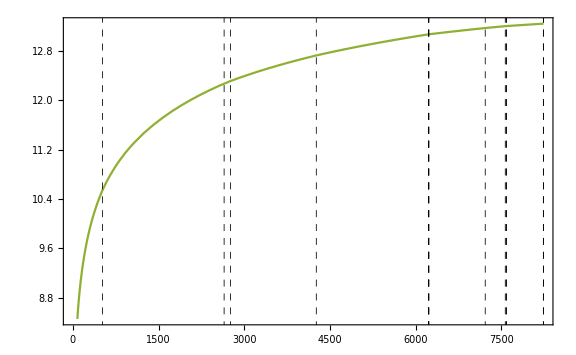

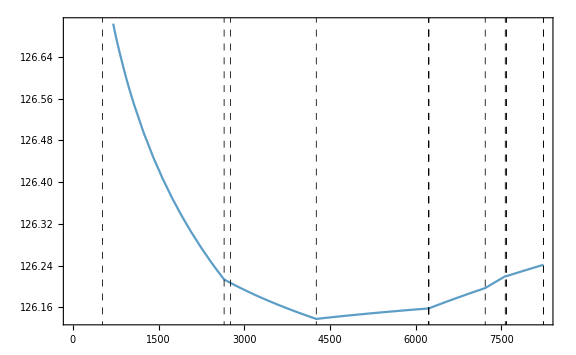

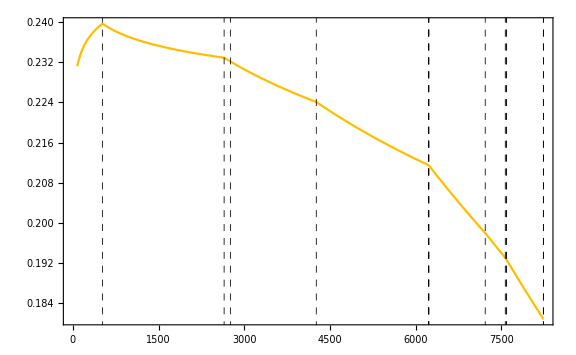

```mathematica
(*Put all the solutions in a list , and make a oredered dictionary with their names and their λ values*)
(*fullList = Sort[Join[λListBottom,λListTau, λListPsiDark]];*)


classDict=<|"Tau"->       <|"Type"->"Fermion", "Sols"->Delete[λListTau,1] , 
					"GSMCharges"-><|"SU3C"->1,"SU2L"->2,  "U1EM"->  <|"QEM" -> -1, "T3"-> -1/2|> |> 
				     |> ,
	               "Bottom"-> <|"Type"->"Fermion", "Sols"->Delete[λListBottom,1], 
					  "GSMCharges"-><|"SU3C"->3,"SU2L"->2,  "U1EM"->  <|"QEM" -> -1/3, "T3"->-1/2|>  |>  
				      |>,
                       "Top"->         <|"Type"->"Fermion", "Sols"->Delete[λListTop,1] , 
					  "GSMCharges"-><|"SU3C"->3, "SU2L"->1, "U1EM"->  <|"QEM" -> 2/3, "T3"-> +1/2|>  |> 
				       |>,
(*******************NEED TO CHECK THE CHARGE ASSIGNMENT/S FOR MPSIDARK*************)
"mPsiDarkUno"->         <|"Type"->"Fermion", "Sols"->Delete[λListPsiDark,1] , 
					  "GSMCharges"-><|"SU3C"->3, "SU2L"->1, "U1EM"->  <|"QEM" -> 2/3, "T3"-> +1/2|>  |> 
				       |>,
"mPsiDarkDos"->         <|"Type"->"Fermion", "Sols"->Delete[λListPsiDark,1] , 
					  "GSMCharges"-><|"SU3C"->3, "SU2L"->1, "U1EM"->  <|"QEM" -> -2/3, "T3"-> -1/2|>  |> 
				       |>,
"mPsiDarkTres"->         <|"Type"->"Fermion", "Sols"->Delete[λListPsiDark,1] , 
					  "GSMCharges"-><|"SU3C"->1, "SU2L"->1, "U1EM"->  <|"QEM" -> -1, "T3"-> -1/2|>  |> 
				       |>,
"mPsiDarkQuatro"->         <|"Type"->"Fermion", "Sols"->Delete[λListPsiDark,1] , 
					  "GSMCharges"-><|"SU3C"->1, "SU2L"->1, "U1EM"->  <|"QEM" -> 0, "T3"-> +1/2|>  |> 
				       |>,
(*******************NEED TO CHECK THE CHARGE ASSIGNMENT/S FOR MPSIDARK*************)


		     (*"W-"->        <|"Type"->"Boson", "Sols"->Delete[λListW,1],
					 "GSMCharges"-><|"SU3C"->1, "U1EM"->  -1 |> 
					|>,*)
		    "Neutrino"-><|"Type"->"Fermion", "Sols"-> Delete[λListν,1],
					    "GSMCharges"-> <|"SU3C"->1, "SU2L"->2, "U1EM"-><|"QEM"-> 0,  "T3"->+1/2|> |>
					|>,
		    "W-"->        <|"Type"->"Boson", "Sols"->Delete[λListW,1],
					 "GSMCharges"-><|"SU3C"->1,"SU2L"->3,  "U1EM"->  <|"QEM" -> -1, "T3"-> -1|>  |> 
					|>,
		    "W+"->        <|"Type"->"Boson", "Sols"->Delete[λListW,1],
					 "GSMCharges"-><|"SU3C"->1,"SU2L"->3,  "U1EM"->  <|"QEM" -> +1, "T3"-> +1|>  |> 
					|>
		(*Z0 doesn't contribute to the running ? since it isn't charged under QEM or T3*)
		(*,"Z0"->        <|"Type"->"Boson", "Sols"->Delete[λListZ,1],
					 "GSMCharges"-><|"SU3C"->1,"SU2L"->1,  "U1EM"->  <|"QEM" -> 0, "T3"-> 0|>  |> 
					|>*)
|>;


dictMerged=<||>;

allPartNames=Keys[classDict];

For [i=1, i≤Length[allPartNames], i++,
partName = allPartNames[[i]];
newDict = makeDictTowers[classDict[[partName]][["Sols"]],partName ];
AppendTo[dictMerged, newDict];
];


orderedTowerDict = SortBy[dictMerged, #&];


couplingDict = <|"SU2L"-> <|"Coupling"-> g2L, "InitBeta"->-19/16, "InitBC"->Sqrt[4π /127.91]/Sqrt[sin2θW]|>, 
			   "SU3C"-><|"Coupling"-> g3C, "InitBeta"->-7, "InitBC" -> Sqrt[4π 0.11822]|>
|>;

solvedRGEdict =<||>;
solvedRGEList ={};
gaugeGroupList = Keys[couplingDict];

For[iGauge=1, iGauge≤ Length[gaugeGroupList], iGauge++,
gaugeGroup = gaugeGroupList[[iGauge]];
gaugeCoupling = couplingDict[[gaugeGroup]][["Coupling"]];
gaugeInitBeta = couplingDict[[gaugeGroup]][["InitBeta"]];
gaugeInitBC = couplingDict[[gaugeGroup]][["InitBC"]];

rgeSystem = makePiecewiseRGE[classDict, gaugeCoupling,gaugeInitBeta,gaugeGroup,  μ, k];
solvedRGE = solvePieceWiseRGE[rgeSystem, gaugeInitBC, gaugeCoupling, μ];

solvedRGEdict[[ gaugeGroup]] = solvedRGE;
AppendTo[solvedRGEList, solvedRGE];

]

(************************************************************************)
initBetaEM=22;
initBetaSin2ThW=-1.0864000000000096;


(************************NEED TO CHECK INITIAL β FUNCTION VALUES FOR αEM Sin θW ***********************)
rgeSystem = makePiecewiseRGE[classDict, α1EM,initBetaEM,"U1EM",  μ, k];
solvedRGEαEM = solvePieceWiseRGE[rgeSystem,Sqrt[4π /127.91] , α1EM, μ];
sin2WSolved = getWeinbergSolvedRGE[solvedRGEαEM, classDict, sin2θW,initBetaSin2ThW, μ];

plotRGEsol[4 π / solvedRGEdict[["SU3C"]]^2, orderedTowerDict, μ, 80 , {"\\frac{4 \\pi}{g^2_{3C}}"}, Automatic, False, {ColorData[97,"ColorList"][[3]]}]

plotRGEsol[{4 π / solvedRGEαEM^2}, orderedTowerDict, μ, 80 , {"\\frac{4 \\pi}{g^2_{EM}}"}
, Automatic, False, ColorData[97,"ColorList"][[7]]
]

plotRGEsol[sin2WSolved, orderedTowerDict, μ, 80 , {"\\sin\\theta_W"},Automatic, True, ColorData[97,"ColorList"][[8]]]


(*plotRGEsol[{4 π / solvedRGEαEM^2, 4 π / solvedRGEdict[["SU3C"]]^2}, orderedTowerDict, μ, 80 , {"\\frac{4 \\pi}{g^2_{EM}}", "\\frac{4 \\pi}{g^2_{3C}}"}]*)
```

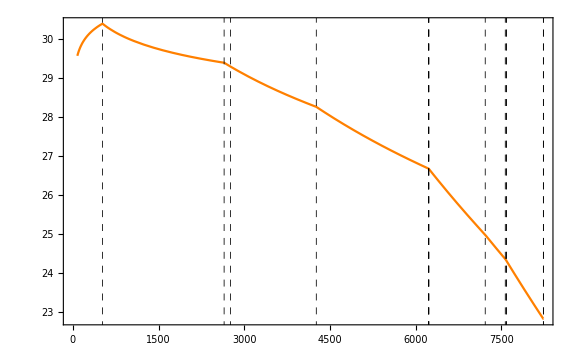

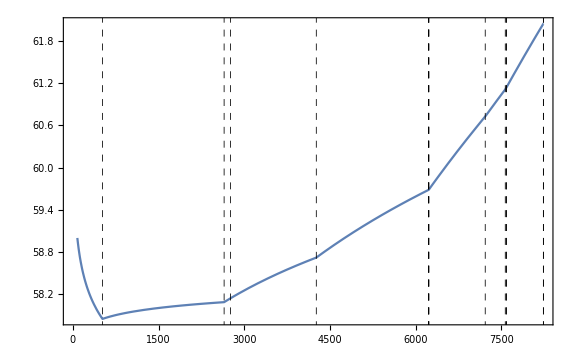

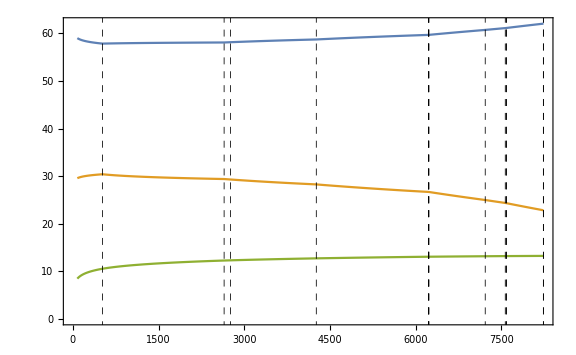

```mathematica
plotRGEsol[sin2WSolved * (4 π / solvedRGEαEM^2), orderedTowerDict, μ, 80 , {"\\frac{4 \\pi}{g^2_{2L}}"}
,Automatic, False, {Orange}
]

plotRGEsol[3/5(1-sin2WSolved) (4 π / solvedRGEαEM^2), orderedTowerDict, μ, 80 , {"\\frac{4 \\pi}{g^2_{1Y}}"}

]
plotRGEsol[{3/5(1-sin2WSolved) (4 π / solvedRGEαEM^2),sin2WSolved * (4 π / solvedRGEαEM^2),4 π / solvedRGEdict[["SU3C"]]^2}, orderedTowerDict, μ, 80 , {"\\frac{4 \\pi}{g^2_{1Y}}", "\\frac{4 \\pi}{g^2_{2L}}","\\frac{4 \\pi}{g^2_{3C}}" }
,Automatic
]
```

```mathematica
(*Getting the boundary conditions for the 5D RGEs*)
α1YatMKK5inv = 3/5(1-sin2WSolved) (4 π / solvedRGEαEM^2)/.{μ->mKK5};
α2LatMKK5inv= sin2WSolved * (4 π / solvedRGEαEM^2)/.{μ->mKK5};
α3CatMKK5inv = 4 π / solvedRGEdict[["SU3C"]]^2 /.{μ-> mKK5};

α4Cinv = α3CatMKK5inv + 1/(12 π);
α2Linv = α2LatMKK5inv;
α2Rinv =5/3 α1YatMKK5inv - 2/3 α3CatMKK5inv + 8/(45 π);
Print[α4Cinv,"  ", α2Linv," ", α2Rinv];
```

### Needed a break here

```mathematica
(*
tauDict = makeDictTowers[Delete[λListTau,1], "Tau"];
bottomDict =makeDictTowers[Delete[λListBottom,1], "Bottom"];
topDict =makeDictTowers[Delete[λListTop,1], "Top"];
WDict = makeDictTowers[Delete[λListW,1], "W+-"];
orderedTowerDict = SortBy[Join[tauDict, bottomDict, WDict, topDict], #&];*)
(*
rgeSystem = makePiecewiseRGE[orderedTowerDict, g1Y,  41/10 , μ];
rgeSystem2 = makePiecewiseRGE[orderedTowerDict, g2L, -19/16 , μ];
rgeSystem3 = makePiecewiseRGE[orderedTowerDict, g3C, -7 , μ];*)
(*Dictionary and list of ordered keys for the solutions*)
(*orderedTowerDict = SortBy[dictMerged, #&];*)
dictMerged=<||>;
allPartNames=Keys[classDict];

For [i=1, i≤Length[allPartNames], i++,
partName = allPartNames[[i]];
newDict = makeDictTowers[classDict[[partName]][["Sols"]],partName ];
AppendTo[dictMerged, newDict];
];
orderedTowerDict = SortBy[dictMerged, #&];




rgeSystem = makePiecewiseRGE[classDict, g1Y,  41/10 ,"SU3C",  μ, k];
rgeSystem2 = makePiecewiseRGE[classDict, g2L,  -19/16,"SU2L",  μ, k];
rgeSystem3 = makePiecewiseRGE[classDict, g3C,  -7,"SU3C",  μ, k];


solvedRGE = solvePieceWiseRGE[rgeSystem, Sqrt[5/3* 4π /127.91]/Sqrt[1-sin2θW], g1Y, μ];
solvedRGE2 = solvePieceWiseRGE[rgeSystem2, Sqrt[4π /127.91]/Sqrt[sin2θW], g2L, μ];
solvedRGE3 = solvePieceWiseRGE[rgeSystem3, Sqrt[4π 0.11822], g3C, μ];

4π/(Sqrt[4π /127.91]/Sqrt[sin2θW])^2
Sqrt[4π /127.91]/Sqrt[1-sin2θW]

plotRGEsol[{4 π/solvedRGE3^2 }, orderedTowerDict, μ, 80 ]
```

```mathematica
(*

startBetaCoeff = 41/10;
(*We start running at Subscript[M, Z]  = 80 GeV*)
startReg = 80; 
βFctU1Y = g1Y[μ]^3/(4π)^2;

newBetaCoeff = addToBetaCoeff[startBetaCoeff, "Fermion"];
newReg = k* λ/. newDict[["Tau2"]];
newReg2 = k* λ/. newDict[["Bottom2"]];

pieceWiseRGE = Piecewise[{{ βFctU1Y*startBetaCoeff, startReg≤μ≤newReg}, {βFctU1Y* newBetaCoeff, newReg≤μ≤newReg2}}];

(*Solve the 1st branch*)
g1YSol =NDSolve[{μ ∂_μ g1Y[μ] ==pieceWiseRGE[[1, 1, 1]], g1Y[startReg]==0.35},{g1Y}, {μ, startReg, newReg}];
(*Get the 1st boundary condition from the edge of the previous solution*)
g1YBc1 = g1Y[μ]/.g1YSol/.{μ->newReg};
(*Solve the 2nd region*)
g1YSol2 = NDSolve[{μ ∂_μ g1Y[μ] ==pieceWiseRGE[[1, 2, 1]], g1Y[newReg]==g1YBc1[[1]]},{g1Y}, {μ, newReg, newReg2}];

pieceWiseRGESoln = Piecewise[ {{g1Y[μ]/.g1YSol[[1, 1]], startReg≤ μ≤newReg}, {g1Y[μ]/.g1YSol2[[1, 1]], newReg≤μ≤newReg2}}];

Plot[pieceWiseRGESoln, {μ, startReg, newReg2},Epilog->{{InfiniteLine[{{newReg,0.0},{newReg,0.5}}],Text[Style["Ψ_D",Black],{newReg+50,0.350}]},{InfiniteLine[{{newReg2,0.0},{newReg2,0.5}}],Text[Style["Ψ_Top",Black],{newReg2-50,0.350}]}}]*)
```

### W, Z tower comparison

```mathematica
Manipulate[
Plot[{WbosonSol, ZbosonSol/.{cos2θW-> cos2θWmanip}}, {λ, 0.0, 0.5}, PlotLegends->"Expressions"]
, {cos2θWmanip, 0.0, 1}
]
(*Note that the 1ts tower for W and Z is almost identical in mass, and similarly the 2nd and so on. The difference gets more noticable for small zL , and if the Weinberg angle evolves to very large values(implicitly the Cos(θW) will be very small). PREVENTITIVE we'l put in th separation of both but we could provisorly put the β function modification to take the full Casimir of SU(2) when crossing the W threshold  *)

Print["Z^(0) tower mass: ", k*λ/.λListZ[[1]]];
Print["W^(0) tower mass: ", k*λ/.λListW[[1]]];
Print["Z^(1) tower mass: ", k*λ/.λListZ[[2]]];
Print["W^(1) tower mass: ", k*λ/.λListW[[2]]];
```

### W_R, (A^(4, 11))_(μ, z) and γ tower comparison

In the below we can see that the λ_γ solution (corresponding to C’, i.e. the orange Line)  is ALWAYS  larger than λ_W_R (corresponding to C, i.e the blue line), so we’re safe to use mKK5 = (π k)/(zL -1) and then run up to k *λ_W_R.  Also λ_Higgs is larger than λ_γ so we don’t really need to worry about it.

```mathematica
Manipulate[
Plot[{Cbasis[λ, 1, zLvar], Cprime[λ ,1, zLvar], Sbasis[λ, 1, zLvar] }, {λ, 0, 0.25}, 
	PlotLegends->"Expressions", PlotRange->{{0, 0.25},{-0.1, 0.1}}],

{zLvar, 1, 500}]
```

### Plotting all the solutions.

```mathematica
mKK5Line = InfiniteLine[{mKK5/k,0},{0,1}];
uSolLine = InfiniteLine[{λ/.λListTop[[1]],0},{0,1}];
psiDarkSolLine =InfiniteLine[{λ/.λListPsiDark[[1]],0},{0,1}];
bottomQuarkSolLine =InfiniteLine[{λ/.λListBottom[[1]],0},{0,1}];
tauSolLine=InfiniteLine[{λ/.λListTau[[1]],0},{0,1}];
wSolLine = InfiniteLine[{λ/.λListW[[1]],0},{0,1}];
wRSolLine = InfiniteLine[{λ/.λListWR[[1]],0},{0,1}];





(*Don't need this since the below are absorbed by W+-, Z0*)
(*Aνa11SolTower = Cprime[λ, z, zLvar]*Sbasis[λ, z, zLvar] + λ (Sin[θHmin])^2/.replacementRules;*)


GraphicsGrid[{
{Plot[{uQuarkSol}, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{{mKK5Line}, {Thick,Red ,uSolLine}}, PlotLabel->"λ_Top Sols.", AxesLabel->Automatic] ,
Plot[{psiDarkQuarkSol}, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{{mKK5Line}, {Thick,Red ,psiDarkSolLine}}, PlotLabel->"λ_ψDark Sols.", AxesLabel->Automatic],
Plot[{bQuarkSol }, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions" ,Epilog->{{mKK5Line}, {Thick,Red ,bottomQuarkSolLine}}, PlotLabel->"λ_Bottom Sols.",AxesLabel->Automatic], Plot[{ tauLeptonSol}, {λ, 0, mKK5/k + π/(4zL)}  , PlotLegends->"Expressions" ,Epilog->{{mKK5Line}, {Thick,Red ,tauSolLine}}, PlotLabel->"λ_Tau Sols.", AxesLabel->Automatic]},

{Plot[{WbosonSol}, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{{mKK5Line}, {Thick,Red ,wSolLine}}, PlotLabel->"λ_(W±) Sols.", AxesLabel->Automatic],
Plot[{ γTower}, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{InfiniteLine[{mKK5/k,0},{0,1}]}, PlotLabel->"λ_γTower Sols.", AxesLabel->Automatic],
Plot[{ WRSol},{λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{{mKK5Line}, {{Thick,Red ,wRSolLine}}}, PlotLabel->"λ_WR Sols.", AxesLabel->Automatic],
Plot[{ HiggsSolTower},{λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions", Epilog->{InfiniteLine[{mKK5/k,0},{0,1}]}, PlotLabel->"λ_Higgs Sols.", AxesLabel->Automatic]},

{Plot[{NeutrinoSol}, {λ, 0, mKK5/k + π/(4zL)} , PlotLegends->"Expressions",  PlotLabel->"λ_ν0 Sols.", Epilog->{InfiniteLine[{mKK5/k,0},{0,1}]},AxesLabel->Automatic]}

}]
```

```mathematica
(*θHmin = 0;*)
Clear[θHmin];
replacementRules = {z->1, c0var->c0, zLvar->zL,   c1var -> c1, μ2TildeVar -> μ2Tilde, μ11PrimeVar -> μ11Prime, c2var -> c2, c0PrimeVar -> c0Prime};
uQuarkSol = SL0 * SR0  + (Sin[θHminVar/2])^2/.replacementRules;
bQuarkSol = SL0 * SR0  + (Sin[θHminVar/2])^2+((μ1var^2) SR0* CR0 * SL1 *CR1)/(μ11var^2 (CR1)^2 - (SL1)^2)/.replacementRules;



Manipulate[
Plot[{uQuarkSol/.{θHminVar->θHminManip},   bQuarkSol/.{θHminVar->θHminManip, μ11var->μ11Manip, μ1var->μ1Manip}}, {λ, 0, 0.15} , PlotLegends->"Expressions",  PlotLabel->"λ_Top Sols.", AxesLabel->Automatic, PlotRange->{{0, 0.15}, {-0.1,0.1}}],
{θHminManip, 0, 0.5}, {μ11Manip, 0, 100}, {μ1Manip, 0, 100}
]
```